#### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"helper_functions.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"dls_mem_functions.nb"}]];
```

#### Data import

The file dls_mass_phot_bsa.txt contains the dls data for 3 mg/mL BSA in HEPES buffer at pH 7.0.

```mathematica
fnd=FileNames["dls*.txt"];
TableForm[%]
```

dls_mass_phot_bsa.txt

The plot below compares the original g₂ data from the Malvern instrument (blue) with the processed g₁ data generated using clipG2toG1.

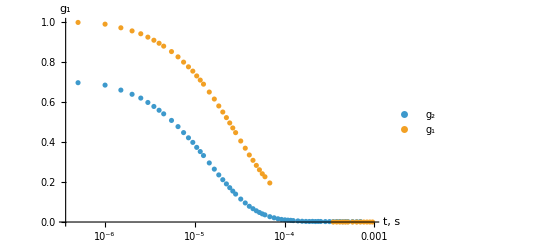

```mathematica
dbsa=N@{10^-6 dlsm[fnd[[1]]][[4,1]],dlsm[fnd[[1]]][[5,1]]}ᵀ;
g1bsac=clipG2toG1[dbsa,16 10^-2,1 10^-4,13];
ListPlot[{Take[dbsa,60],g1bsac},ScalingFunctions->{"Log"},PlotRange->All,PlotLegends->{"g_2","g_1"},AxesLabel->{"t, s", "g_1"}]
```

Feasibility boundary constant C_b for BSA, determined experimentally as the value at which dlsMEMc converges.

```mathematica
cbsab=0.0024;
```

Running constrained MEM for two values of C_b.

```mathematica
Timing[outc=Quiet[dlsMEMc[g1bsac,0.02,(# cbsab)]&/@{1.,2.}];]
```

{31.9581,Null}

Recovered distributions for two values of C_(b.)

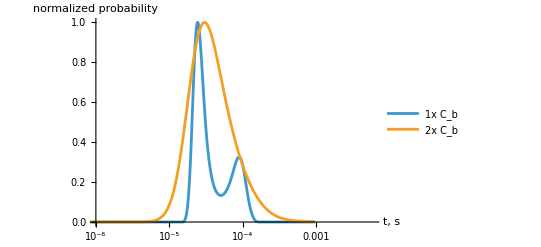

```mathematica
ListLinePlot[{(#[[1]])^-1,(#[[2]])/Max[#[[2]]]}ᵀ&/@outc,ScalingFunctions->{"Log"},PlotRange->{{0.1 10^-5,0.6 10^-2},All},AxesLabel->{"t, s", "normalized probability"},PlotLegends->{"1x C_b","2x C_b"}]
```